# Pockel’s Cell Laser Feedback

The Jones Matrix for a retarder with a phase shift of ϕ  can be written as:

```mathematica
J0[ϕ_] := {{Exp[ⅈ*ϕ/2],0},{0,Exp[-ⅈ*ϕ/2]}}
J0[ϕ]//MatrixForm
```

(ⅇ^((ⅈ ϕ)/2) | 0
0 | ⅇ^(-(ⅈ ϕ)/2))

If you rotate the retarder by θ, you get the correction:

```mathematica
J1[ϕ_,θ_]:= {{Cos[ϕ/2]+ⅈ*Sin[ϕ/2]*Cos[2*θ], ⅈ*Sin[ϕ/2]*Sin[2*θ]},{ⅈ*Sin[ϕ/2]*Sin[2*θ],Cos[ϕ/2]-ⅈ*Sin[ϕ/2]*Cos[2*θ]}}
J1[ϕ,θ]//MatrixForm
```

(Cos[ϕ/2]+ⅈ Cos[2 θ] Sin[ϕ/2] | ⅈ Sin[2 θ] Sin[ϕ/2]
ⅈ Sin[2 θ] Sin[ϕ/2] | Cos[ϕ/2]-ⅈ Cos[2 θ] Sin[ϕ/2])

By placing the pockels cell in between two polarizing beam splitter cubes (note that the power is maximized out of the first PBS)

```mathematica
Jtot[a_,b_]:= {{1,0},{0,0}}.J1[a,b].{{1,0},{0,0}}
Jtot[ϕ,θ]//MatrixForm
```

(Cos[ϕ/2]+ⅈ Cos[2 θ] Sin[ϕ/2] | 0
0 | 0)

```mathematica
Efield = {1,0}
Eprime[ϕ_,θ_] :=Jtot[ϕ,θ].Efield
```

{1,0}

```mathematica
$Assumptions = {Element[{ϕ,θ},Reals]}
Intensity[ϕ_,θ_] := Eprime[ϕ,θ]†.Eprime[ϕ,θ]
FullSimplify[Expand[Intensity[ϕ,θ]]]
```

{(ϕ|θ)∈ℝ}

Cos[ϕ/2]^2+Cos[2 θ]^2 Sin[ϕ/2]^2

```mathematica
Solve[FullSimplify[Intensity[ϕ,θ]]==1]
```

{{θ→ConditionalExpression[π C[1], ϕ∈ℝ&&C[1]∈ℤ]},{θ→ConditionalExpression[1/2 (-π+2 π C[1]), ϕ∈ℝ&&C[1]∈ℤ]},{θ→ConditionalExpression[1/2 (π+2 π C[1]), ϕ∈ℝ&&C[1]∈ℤ]},{ϕ→ConditionalExpression[4 π C[1], ]},{ϕ→ConditionalExpression[2 (π+2 π C[1]), ]}}

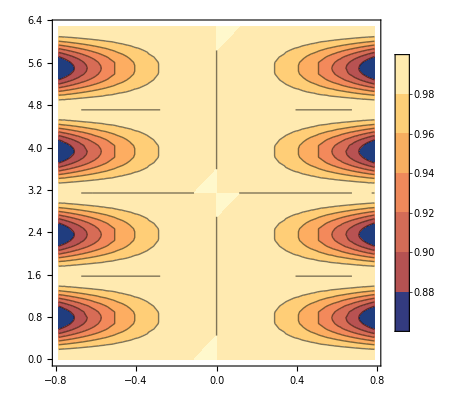

```mathematica
ContourPlot[Intensity[x,y],{x,-π/4,π/4},{y,0,2π},PlotLegends->Automatic]
```

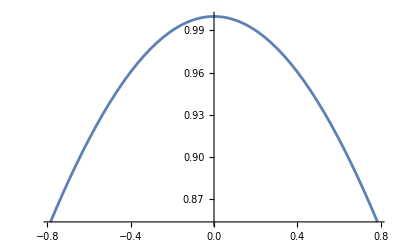

```mathematica
Plot[Intensity[x,π/4],{x,-π/4,π/4}]
```

We don’t want to have to apply the quarter wave voltage to the pockels cell though. We want to keep it below 500V to not deal with scary HV cables. Note that pockels cells are linear so if λ/4 = 3.2kV then the phase at 500V is:

```mathematica
lambda = π/2 *0.5/3.2
RootApproximant[lambda,1]
N[π/2]
```

0.245437

10695401/43576984

1.5708

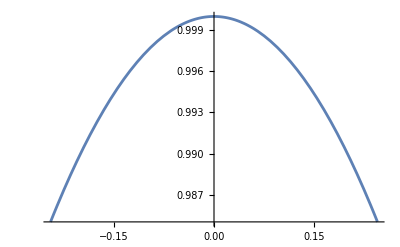

```mathematica
Plot[Intensity[x,π/4],{x,-lambda,lambda}]
```

To do this, we can put in a waveplate.
With a λ/2 waveplate we get:

```mathematica
Jtot2[ϕ_,θ_,ψ_]:= {{1,0},{0,0}}.J1[ϕ,θ].J1[π,ψ].{{1,0},{0,0}}
Jtot2[ϕ,θ,ψ]//MatrixForm
```

(ⅈ Cos[2 ψ] (Cos[ϕ/2]+ⅈ Cos[2 θ] Sin[ϕ/2])-Sin[2 θ] Sin[ϕ/2] Sin[2 ψ] | 0
0 | 0)

```mathematica
Efield = {1,0}
Eprime2[ϕ_,θ_,ψ_] :=Jtot2[ϕ,θ,ψ].Efield
$Assumptions = {Element[{ϕ,θ,ψ},Reals]}
Intensity2[ϕ_,θ_,ψ_] := Eprime2[ϕ,θ,ψ]†.Eprime2[ϕ,θ,ψ]
FullSimplify[Expand[Intensity2[ϕ,θ,ψ]]]
```

{1,0}

{(ϕ|θ|ψ)∈ℝ}

Cos[ϕ/2]^2 Cos[2 ψ]^2+Cos[2 θ-2 ψ]^2 Sin[ϕ/2]^2

```mathematica
ContourPlot[Intensity2[x,π/4,y],{x,-π/4,π/4},{y,0,2π},PlotLegends->Automatic]
```

-Graphics-

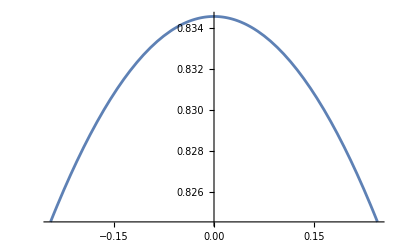

```mathematica
Plot[Intensity2[x,π/4,π/15],{x,-lambda,lambda}]
```

If using λ/4 waveplate instead:

```mathematica
Jtot3[ϕ_,θ_,ψ_]:= {{1,0},{0,0}}.J1[ϕ,θ].J1[π/2,ψ].{{1,0},{0,0}}
Jtot3[ϕ,θ,ψ]//MatrixForm
Efield = {1,0}
Eprime3[ϕ_,θ_,ψ_] :=Jtot3[ϕ,θ,ψ].Efield
$Assumptions = {Element[{ϕ,θ,ψ,ξ},Reals]}
Intensity3[ϕ_,θ_,ψ_] := Eprime3[ϕ,θ,ψ]†.Eprime3[ϕ,θ,ψ]
FullSimplify[Expand[Intensity3[ϕ,θ,ψ]]]
```

((1/(√2)+(ⅈ Cos[2 ψ])/(√2)) (Cos[ϕ/2]+ⅈ Cos[2 θ] Sin[ϕ/2])-(Sin[2 θ] Sin[ϕ/2] Sin[2 ψ])/(√2) | 0
0 | 0)

{1,0}

{(ϕ|θ|ψ|ξ)∈ℝ}

1/8 (5-Cos[4 θ] (-1+Cos[ϕ])+Cos[ϕ]+Cos[4 θ-4 ψ]+Cos[4 ψ]+2 Sin[2 θ] (Cos[ϕ] Sin[2 θ-4 ψ]-2 Sin[ϕ] Sin[2 ψ]))

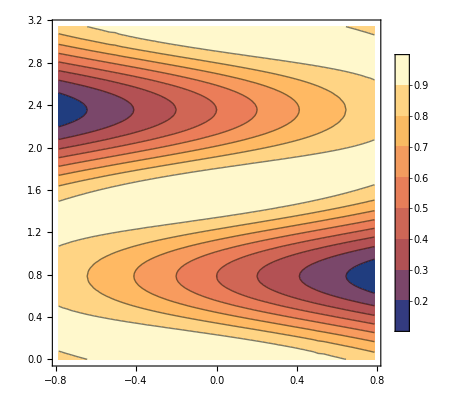

```mathematica
ContourPlot[Intensity3[x,π/4 ,y],{x,-π/4,π/4},{y,0,π},PlotLegends->Automatic]
```

```mathematica
ContourPlot3D[Intensity3[x ,y,z],{x,-π/4,π/4},{y,0,π/2},{z,0,π/2}]
```

-Graphics3D-

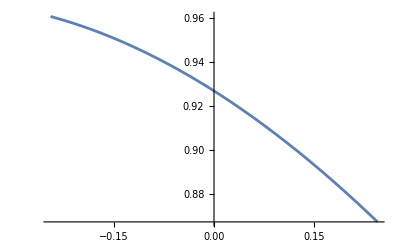

```mathematica
Plot[Intensity3[x,π/4,π/16],{x,-lambda,lambda}]
```

Here we can increase and decrease power with feedback, which means we can sit at 0V and just apply an AC feedback signal.

To align this, rotate the cell and waveplate to let a small amount of light be deflected by the PBS. Then apply a ±500V AC signal to make sure that it modulates the light coming out. Note that the second PBS CANNOT be used to stabilize the beam. You will drive all of the noise into the polarization we care about. Another λ/2 waveplate and PBS must be downstream to pick off some light.

```mathematica
"Rotating the PBS relative to each other gets you:"
Jtot4[ϕ_,θ_,ψ_]:= {{1,0},{0,0}}.J1[ϕ,θ].J1[π/2,ψ].{{0,0},{0,1}}
Jtot4[ϕ,θ,ψ]//MatrixForm
Efield = {0,1}
Eprime4[ϕ_,θ_,ψ_] :=Jtot4[ϕ,θ,ψ].Efield
$Assumptions = {Element[{ϕ,θ,ψ},Reals]}
Intensity4[ϕ_,θ_,ψ_] := Eprime4[ϕ,θ,ψ]†.Eprime4[ϕ,θ,ψ]
FullSimplify[Expand[Intensity4[ϕ,θ,ψ]]]
```

Rotating the PBS relative to each other gets you:

(0 | ⅈ (1/(√2)-(ⅈ Cos[2 ψ])/(√2)) Sin[2 θ] Sin[ϕ/2]+(ⅈ (Cos[ϕ/2]+ⅈ Cos[2 θ] Sin[ϕ/2]) Sin[2 ψ])/(√2)
0 | 0)

{0,1}

{(ϕ|θ|ψ)∈ℝ}

1/2 (Sin[ϕ/2]^2 (Sin[2 θ]^2+Sin[2 θ-2 ψ]^2)+Sin[2 θ] Sin[ϕ] Sin[2 ψ]+Cos[ϕ/2]^2 Sin[2 ψ]^2)

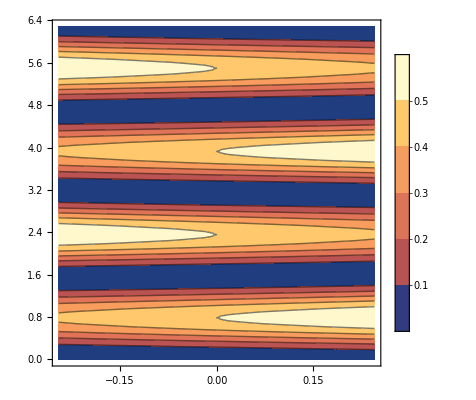

```mathematica
ContourPlot[Intensity4[x,π/8,y],{x,-lambda,lambda},{y,0,2π},PlotLegends->Automatic]
```

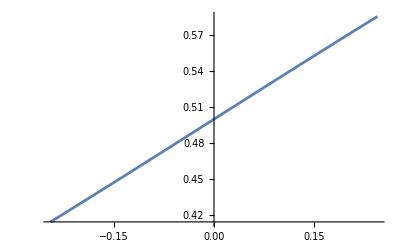

```mathematica
Plot[Intensity4[x,π/8,π/4],{x,-lambda,lambda}]
```

As expected, if the PBS are orthogonal to each other, the maximum power output is only ~50%